# Analyzing Economic Trends: A Comparative Study of State-Space Models and Neural Networks

Muhammad Ali Hafeez

Abstract

## Introduction

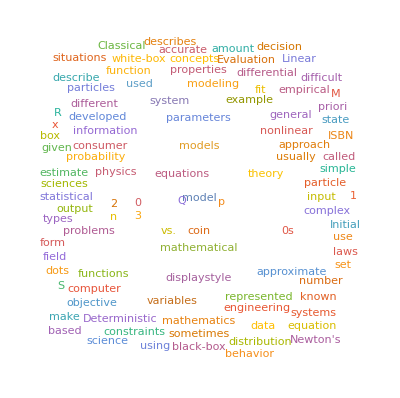

```mathematica
WordCloud[WikipediaData["Mathematical Modeling"]]
```

The purpose of this essay is to introduce a highly significant discussion. The emergence of machine learning has brought about groundbreaking advancements. However, have we thoroughly analyzed each technique in terms of their predictive power relative to one another? This essay aims to compare two crucial techniques: State-Space Models, specifically those employing the Kalman filter, and Neural Networks, which represent a more contemporary approach.

## Data

The data that will be used in this computational essay is the Federal Reserve of Economic Data (FRED) Real Gross Domestic Product data from 1947 to 2023.

```mathematica
data=Import["C:\\Users\\ali12\\Downloads\\GDP.xls"];
preprocessedData=data/. Null->""; 
splitData=Partition[Flatten[preprocessedData],2];
table=Grid[splitData,Alignment->Center]//DisplayForm;
styledTable=StyleBox[table,GridBoxOptions->{GridBoxDividers->{"Columns"->True},GridBoxItemStyle->{"ColumnBands"->{{1,1}->Bold},"Columns"->{2->Bold}}}];
scrollableTable=Pane[styledTable,ImageSize->{Automatic,300},Scrollbars->True];
scrollableTable
```

StyleBox[FRED Graph Observations | 
Federal Reserve Economic Data | 
Link: https://fred.stlouisfed.org | 
Help: https://fredhelp.stlouisfed.org | 
Economic Research Division | 
Federal Reserve Bank of St. Louis | 
 | 
GDP | Gross Domestic Product, Billions of Dollars, Quarterly, Seasonally Adjusted Annual Rate
 | 
Frequency: Quarterly | 
observation_date | GDP
Wed 1 Jan 1947 00:00:00GMT-4 | 243.164
Tue 1 Apr 1947 00:00:00GMT-4 | 245.968
Tue 1 Jul 1947 00:00:00GMT-4 | 249.585
Wed 1 Oct 1947 00:00:00GMT-4 | 259.745
Thu 1 Jan 1948 00:00:00GMT-4 | 265.742
Thu 1 Apr 1948 00:00:00GMT-4 | 272.567
Thu 1 Jul 1948 00:00:00GMT-4 | 279.196
Fri 1 Oct 1948 00:00:00GMT-4 | 280.366
Sat 1 Jan 1949 00:00:00GMT-4 | 275.034
Fri 1 Apr 1949 00:00:00GMT-4 | 271.351
Fri 1 Jul 1949 00:00:00GMT-4 | 272.889
Sat 1 Oct 1949 00:00:00GMT-4 | 270.627
Sun 1 Jan 1950 00:00:00GMT-4 | 280.828
Sat 1 Apr 1950 00:00:00GMT-4 | 290.383
Sat 1 Jul 1950 00:00:00GMT-4 | 308.153
Sun 1 Oct 1950 00:00:00GMT-4 | 319.945
Mon 1 Jan 1951 00:00:00GMT-4 | 336.
Sun 1 Apr 1951 00:00:00GMT-4 | 344.09
Sun 1 Jul 1951 00:00:00GMT-4 | 351.385
Mon 1 Oct 1951 00:00:00GMT-4 | 356.178
Tue 1 Jan 1952 00:00:00GMT-4 | 359.82
Tue 1 Apr 1952 00:00:00GMT-4 | 361.03
Tue 1 Jul 1952 00:00:00GMT-4 | 367.701
Wed 1 Oct 1952 00:00:00GMT-4 | 380.812
Thu 1 Jan 1953 00:00:00GMT-4 | 387.98
Wed 1 Apr 1953 00:00:00GMT-4 | 391.749
Wed 1 Jul 1953 00:00:00GMT-4 | 391.171
Thu 1 Oct 1953 00:00:00GMT-4 | 385.97
Fri 1 Jan 1954 00:00:00GMT-4 | 385.345
Thu 1 Apr 1954 00:00:00GMT-4 | 386.121
Thu 1 Jul 1954 00:00:00GMT-4 | 390.996
Fri 1 Oct 1954 00:00:00GMT-4 | 399.734
Sat 1 Jan 1955 00:00:00GMT-4 | 413.073
Fri 1 Apr 1955 00:00:00GMT-4 | 421.532
Fri 1 Jul 1955 00:00:00GMT-4 | 430.221
Sat 1 Oct 1955 00:00:00GMT-4 | 437.092
Sun 1 Jan 1956 00:00:00GMT-4 | 439.746
Sun 1 Apr 1956 00:00:00GMT-4 | 446.01
Sun 1 Jul 1956 00:00:00GMT-4 | 451.191
Mon 1 Oct 1956 00:00:00GMT-4 | 460.463
Tue 1 Jan 1957 00:00:00GMT-4 | 469.779
Mon 1 Apr 1957 00:00:00GMT-4 | 472.025
Mon 1 Jul 1957 00:00:00GMT-4 | 479.49
Tue 1 Oct 1957 00:00:00GMT-4 | 474.864
Wed 1 Jan 1958 00:00:00GMT-4 | 467.54
Tue 1 Apr 1958 00:00:00GMT-4 | 471.978
Tue 1 Jul 1958 00:00:00GMT-4 | 485.841
Wed 1 Oct 1958 00:00:00GMT-4 | 499.555
Thu 1 Jan 1959 00:00:00GMT-4 | 510.33
Wed 1 Apr 1959 00:00:00GMT-4 | 522.653
Wed 1 Jul 1959 00:00:00GMT-4 | 525.034
Thu 1 Oct 1959 00:00:00GMT-4 | 528.6
Fri 1 Jan 1960 00:00:00GMT-4 | 542.648
Fri 1 Apr 1960 00:00:00GMT-4 | 541.08
Fri 1 Jul 1960 00:00:00GMT-4 | 545.604
Sat 1 Oct 1960 00:00:00GMT-4 | 540.197
Sun 1 Jan 1961 00:00:00GMT-4 | 545.018
Sat 1 Apr 1961 00:00:00GMT-4 | 555.545
Sat 1 Jul 1961 00:00:00GMT-4 | 567.664
Sun 1 Oct 1961 00:00:00GMT-4 | 580.612
Mon 1 Jan 1962 00:00:00GMT-4 | 594.013
Sun 1 Apr 1962 00:00:00GMT-4 | 600.366
Sun 1 Jul 1962 00:00:00GMT-4 | 609.027
Mon 1 Oct 1962 00:00:00GMT-4 | 612.28
Tue 1 Jan 1963 00:00:00GMT-4 | 621.672
Mon 1 Apr 1963 00:00:00GMT-4 | 629.752
Mon 1 Jul 1963 00:00:00GMT-4 | 644.444
Tue 1 Oct 1963 00:00:00GMT-4 | 653.938
Wed 1 Jan 1964 00:00:00GMT-4 | 669.822
Wed 1 Apr 1964 00:00:00GMT-4 | 678.674
Wed 1 Jul 1964 00:00:00GMT-4 | 692.031
Thu 1 Oct 1964 00:00:00GMT-4 | 697.319
Fri 1 Jan 1965 00:00:00GMT-4 | 717.79
Thu 1 Apr 1965 00:00:00GMT-4 | 730.191
Thu 1 Jul 1965 00:00:00GMT-4 | 749.323
Fri 1 Oct 1965 00:00:00GMT-4 | 771.857
Sat 1 Jan 1966 00:00:00GMT-4 | 795.734
Fri 1 Apr 1966 00:00:00GMT-4 | 804.981
Fri 1 Jul 1966 00:00:00GMT-4 | 819.638
Sat 1 Oct 1966 00:00:00GMT-4 | 833.302
Sun 1 Jan 1967 00:00:00GMT-4 | 844.17
Sat 1 Apr 1967 00:00:00GMT-4 | 848.983
Sat 1 Jul 1967 00:00:00GMT-4 | 865.233
Sun 1 Oct 1967 00:00:00GMT-4 | 881.439
Mon 1 Jan 1968 00:00:00GMT-4 | 909.387
Mon 1 Apr 1968 00:00:00GMT-4 | 934.344
Mon 1 Jul 1968 00:00:00GMT-4 | 950.825
Tue 1 Oct 1968 00:00:00GMT-4 | 968.03
Wed 1 Jan 1969 00:00:00GMT-4 | 993.337
Tue 1 Apr 1969 00:00:00GMT-4 | 1009.02
Tue 1 Jul 1969 00:00:00GMT-4 | 1029.96
Wed 1 Oct 1969 00:00:00GMT-4 | 1038.15
Thu 1 Jan 1970 00:00:00GMT-4 | 1051.2
Wed 1 Apr 1970 00:00:00GMT-4 | 1067.38
Wed 1 Jul 1970 00:00:00GMT-4 | 1086.06
Thu 1 Oct 1970 00:00:00GMT-4 | 1088.61
Fri 1 Jan 1971 00:00:00GMT-4 | 1135.16
Thu 1 Apr 1971 00:00:00GMT-4 | 1156.27
Thu 1 Jul 1971 00:00:00GMT-4 | 1177.68
Fri 1 Oct 1971 00:00:00GMT-4 | 1190.3
Sat 1 Jan 1972 00:00:00GMT-4 | 1230.61
Sat 1 Apr 1972 00:00:00GMT-4 | 1266.37
Sat 1 Jul 1972 00:00:00GMT-4 | 1290.57
Sun 1 Oct 1972 00:00:00GMT-4 | 1328.9
Mon 1 Jan 1973 00:00:00GMT-4 | 1377.49
Sun 1 Apr 1973 00:00:00GMT-4 | 1413.89
Sun 1 Jul 1973 00:00:00GMT-4 | 1433.84
Mon 1 Oct 1973 00:00:00GMT-4 | 1476.29
Tue 1 Jan 1974 00:00:00GMT-4 | 1491.21
Mon 1 Apr 1974 00:00:00GMT-4 | 1530.06
Mon 1 Jul 1974 00:00:00GMT-4 | 1560.03
Tue 1 Oct 1974 00:00:00GMT-4 | 1599.68
Wed 1 Jan 1975 00:00:00GMT-4 | 1616.12
Tue 1 Apr 1975 00:00:00GMT-4 | 1651.85
Tue 1 Jul 1975 00:00:00GMT-4 | 1709.82
Wed 1 Oct 1975 00:00:00GMT-4 | 1761.83
Thu 1 Jan 1976 00:00:00GMT-4 | 1820.49
Thu 1 Apr 1976 00:00:00GMT-4 | 1852.33
Thu 1 Jul 1976 00:00:00GMT-4 | 1886.56
Fri 1 Oct 1976 00:00:00GMT-4 | 1934.27
Sat 1 Jan 1977 00:00:00GMT-4 | 1988.65
Fri 1 Apr 1977 00:00:00GMT-4 | 2055.91
Fri 1 Jul 1977 00:00:00GMT-4 | 2118.47
Sat 1 Oct 1977 00:00:00GMT-4 | 2164.27
Sun 1 Jan 1978 00:00:00GMT-4 | 2202.76
Sat 1 Apr 1978 00:00:00GMT-4 | 2331.63
Sat 1 Jul 1978 00:00:00GMT-4 | 2395.05
Sun 1 Oct 1978 00:00:00GMT-4 | 2476.95
Mon 1 Jan 1979 00:00:00GMT-4 | 2526.61
Sun 1 Apr 1979 00:00:00GMT-4 | 2591.25
Sun 1 Jul 1979 00:00:00GMT-4 | 2667.57
Mon 1 Oct 1979 00:00:00GMT-4 | 2723.88
Tue 1 Jan 1980 00:00:00GMT-4 | 2789.84
Tue 1 Apr 1980 00:00:00GMT-4 | 2797.35
Tue 1 Jul 1980 00:00:00GMT-4 | 2856.48
Wed 1 Oct 1980 00:00:00GMT-4 | 2985.56
Thu 1 Jan 1981 00:00:00GMT-4 | 3124.21
Wed 1 Apr 1981 00:00:00GMT-4 | 3162.53
Wed 1 Jul 1981 00:00:00GMT-4 | 3260.61
Thu 1 Oct 1981 00:00:00GMT-4 | 3280.82
Fri 1 Jan 1982 00:00:00GMT-4 | 3274.3
Thu 1 Apr 1982 00:00:00GMT-4 | 3331.97
Thu 1 Jul 1982 00:00:00GMT-4 | 3366.32
Fri 1 Oct 1982 00:00:00GMT-4 | 3402.56
Sat 1 Jan 1983 00:00:00GMT-4 | 3473.41
Fri 1 Apr 1983 00:00:00GMT-4 | 3578.85
Fri 1 Jul 1983 00:00:00GMT-4 | 3689.18
Sat 1 Oct 1983 00:00:00GMT-4 | 3794.71
Sun 1 Jan 1984 00:00:00GMT-4 | 3908.05
Sun 1 Apr 1984 00:00:00GMT-4 | 4009.6
Sun 1 Jul 1984 00:00:00GMT-4 | 4084.25
Mon 1 Oct 1984 00:00:00GMT-4 | 4148.55
Tue 1 Jan 1985 00:00:00GMT-4 | 4230.17
Mon 1 Apr 1985 00:00:00GMT-4 | 4294.89
Mon 1 Jul 1985 00:00:00GMT-4 | 4386.77
Tue 1 Oct 1985 00:00:00GMT-4 | 4444.09
Wed 1 Jan 1986 00:00:00GMT-4 | 4507.89
Tue 1 Apr 1986 00:00:00GMT-4 | 4545.34
Tue 1 Jul 1986 00:00:00GMT-4 | 4607.67
Wed 1 Oct 1986 00:00:00GMT-4 | 4657.63
Thu 1 Jan 1987 00:00:00GMT-4 | 4722.16
Wed 1 Apr 1987 00:00:00GMT-4 | 4806.16
Wed 1 Jul 1987 00:00:00GMT-4 | 4884.56
Thu 1 Oct 1987 00:00:00GMT-4 | 5007.99
Fri 1 Jan 1988 00:00:00GMT-4 | 5073.37
Fri 1 Apr 1988 00:00:00GMT-4 | 5190.04
Fri 1 Jul 1988 00:00:00GMT-4 | 5282.84
Sat 1 Oct 1988 00:00:00GMT-4 | 5399.51
Sun 1 Jan 1989 00:00:00GMT-4 | 5511.25
Sat 1 Apr 1989 00:00:00GMT-4 | 5612.46
Sat 1 Jul 1989 00:00:00GMT-4 | 5695.37
Sun 1 Oct 1989 00:00:00GMT-4 | 5747.24
Mon 1 Jan 1990 00:00:00GMT-4 | 5872.7
Sun 1 Apr 1990 00:00:00GMT-4 | 5960.03
Sun 1 Jul 1990 00:00:00GMT-4 | 6015.12
Mon 1 Oct 1990 00:00:00GMT-4 | 6004.73
Tue 1 Jan 1991 00:00:00GMT-4 | 6035.18
Mon 1 Apr 1991 00:00:00GMT-4 | 6126.86
Mon 1 Jul 1991 00:00:00GMT-4 | 6205.94
Tue 1 Oct 1991 00:00:00GMT-4 | 6264.54
Wed 1 Jan 1992 00:00:00GMT-4 | 6363.1
Wed 1 Apr 1992 00:00:00GMT-4 | 6470.76
Wed 1 Jul 1992 00:00:00GMT-4 | 6566.64
Thu 1 Oct 1992 00:00:00GMT-4 | 6680.8
Fri 1 Jan 1993 00:00:00GMT-4 | 6729.46
Thu 1 Apr 1993 00:00:00GMT-4 | 6808.94
Thu 1 Jul 1993 00:00:00GMT-4 | 6882.1
Fri 1 Oct 1993 00:00:00GMT-4 | 7013.74
Sat 1 Jan 1994 00:00:00GMT-4 | 7115.65
Fri 1 Apr 1994 00:00:00GMT-4 | 7246.93
Fri 1 Jul 1994 00:00:00GMT-4 | 7331.08
Sat 1 Oct 1994 00:00:00GMT-4 | 7455.29
Sun 1 Jan 1995 00:00:00GMT-4 | 7522.29
Sat 1 Apr 1995 00:00:00GMT-4 | 7581.
Sat 1 Jul 1995 00:00:00GMT-4 | 7683.13
Sun 1 Oct 1995 00:00:00GMT-4 | 7772.59
Mon 1 Jan 1996 00:00:00GMT-4 | 7868.47
Mon 1 Apr 1996 00:00:00GMT-4 | 8032.84
Mon 1 Jul 1996 00:00:00GMT-4 | 8131.41
Tue 1 Oct 1996 00:00:00GMT-4 | 8259.77
Wed 1 Jan 1997 00:00:00GMT-4 | 8362.66
Tue 1 Apr 1997 00:00:00GMT-4 | 8518.83
Tue 1 Jul 1997 00:00:00GMT-4 | 8662.82
Wed 1 Oct 1997 00:00:00GMT-4 | 8765.91
Thu 1 Jan 1998 00:00:00GMT-4 | 8866.48
Wed 1 Apr 1998 00:00:00GMT-4 | 8969.7
Wed 1 Jul 1998 00:00:00GMT-4 | 9121.1
Thu 1 Oct 1998 00:00:00GMT-4 | 9293.99
Fri 1 Jan 1999 00:00:00GMT-4 | 9411.68
Thu 1 Apr 1999 00:00:00GMT-4 | 9526.21
Thu 1 Jul 1999 00:00:00GMT-4 | 9686.63
Fri 1 Oct 1999 00:00:00GMT-4 | 9900.17
Sat 1 Jan 2000 00:00:00GMT-4 | 10002.2
Sat 1 Apr 2000 00:00:00GMT-4 | 10247.7
Sat 1 Jul 2000 00:00:00GMT-4 | 10318.2
Sun 1 Oct 2000 00:00:00GMT-4 | 10435.7
Mon 1 Jan 2001 00:00:00GMT-4 | 10470.2
Sun 1 Apr 2001 00:00:00GMT-4 | 10599.
Sun 1 Jul 2001 00:00:00GMT-4 | 10598.
Mon 1 Oct 2001 00:00:00GMT-4 | 10660.5
Tue 1 Jan 2002 00:00:00GMT-4 | 10783.5
Mon 1 Apr 2002 00:00:00GMT-4 | 10887.5
Mon 1 Jul 2002 00:00:00GMT-4 | 10984.
Tue 1 Oct 2002 00:00:00GMT-4 | 11061.4
Wed 1 Jan 2003 00:00:00GMT-4 | 11174.1
Tue 1 Apr 2003 00:00:00GMT-4 | 11312.8
Tue 1 Jul 2003 00:00:00GMT-4 | 11566.7
Wed 1 Oct 2003 00:00:00GMT-4 | 11772.2
Thu 1 Jan 2004 00:00:00GMT-4 | 11923.4
Thu 1 Apr 2004 00:00:00GMT-4 | 12112.8
Thu 1 Jul 2004 00:00:00GMT-4 | 12305.3
Fri 1 Oct 2004 00:00:00GMT-4 | 12527.2
Sat 1 Jan 2005 00:00:00GMT-4 | 12767.3
Fri 1 Apr 2005 00:00:00GMT-4 | 12922.7
Fri 1 Jul 2005 00:00:00GMT-4 | 13142.6
Sat 1 Oct 2005 00:00:00GMT-4 | 13324.2
Sun 1 Jan 2006 00:00:00GMT-4 | 13599.2
Sat 1 Apr 2006 00:00:00GMT-4 | 13753.4
Sat 1 Jul 2006 00:00:00GMT-4 | 13870.2
Sun 1 Oct 2006 00:00:00GMT-4 | 14039.6
Mon 1 Jan 2007 00:00:00GMT-4 | 14215.7
Sun 1 Apr 2007 00:00:00GMT-4 | 14402.1
Sun 1 Jul 2007 00:00:00GMT-4 | 14564.1
Mon 1 Oct 2007 00:00:00GMT-4 | 14715.1
Tue 1 Jan 2008 00:00:00GMT-4 | 14706.5
Tue 1 Apr 2008 00:00:00GMT-4 | 14865.7
Tue 1 Jul 2008 00:00:00GMT-4 | 14899.
Wed 1 Oct 2008 00:00:00GMT-4 | 14608.2
Thu 1 Jan 2009 00:00:00GMT-4 | 14430.9
Wed 1 Apr 2009 00:00:00GMT-4 | 14381.2
Wed 1 Jul 2009 00:00:00GMT-4 | 14448.9
Thu 1 Oct 2009 00:00:00GMT-4 | 14651.2
Fri 1 Jan 2010 00:00:00GMT-4 | 14764.6
Thu 1 Apr 2010 00:00:00GMT-4 | 14980.2
Thu 1 Jul 2010 00:00:00GMT-4 | 15141.6
Fri 1 Oct 2010 00:00:00GMT-4 | 15309.5
Sat 1 Jan 2011 00:00:00GMT-4 | 15351.4
Fri 1 Apr 2011 00:00:00GMT-4 | 15557.5
Fri 1 Jul 2011 00:00:00GMT-4 | 15647.7
Sat 1 Oct 2011 00:00:00GMT-4 | 15842.3
Sun 1 Jan 2012 00:00:00GMT-4 | 16068.8
Sun 1 Apr 2012 00:00:00GMT-4 | 16207.1
Sun 1 Jul 2012 00:00:00GMT-4 | 16319.5
Mon 1 Oct 2012 00:00:00GMT-4 | 16420.4
Tue 1 Jan 2013 00:00:00GMT-4 | 16629.1
Mon 1 Apr 2013 00:00:00GMT-4 | 16699.6
Mon 1 Jul 2013 00:00:00GMT-4 | 16911.1
Tue 1 Oct 2013 00:00:00GMT-4 | 17133.1
Wed 1 Jan 2014 00:00:00GMT-4 | 17144.3
Tue 1 Apr 2014 00:00:00GMT-4 | 17462.7
Tue 1 Jul 2014 00:00:00GMT-4 | 17743.2
Wed 1 Oct 2014 00:00:00GMT-4 | 17852.5
Thu 1 Jan 2015 00:00:00GMT-4 | 17991.3
Wed 1 Apr 2015 00:00:00GMT-4 | 18193.7
Wed 1 Jul 2015 00:00:00GMT-4 | 18307.
Thu 1 Oct 2015 00:00:00GMT-4 | 18332.1
Fri 1 Jan 2016 00:00:00GMT-4 | 18425.3
Fri 1 Apr 2016 00:00:00GMT-4 | 18611.6
Fri 1 Jul 2016 00:00:00GMT-4 | 18775.5
Sat 1 Oct 2016 00:00:00GMT-4 | 18968.
Sun 1 Jan 2017 00:00:00GMT-4 | 19148.2
Sat 1 Apr 2017 00:00:00GMT-4 | 19304.5
Sat 1 Jul 2017 00:00:00GMT-4 | 19561.9
Sun 1 Oct 2017 00:00:00GMT-4 | 19894.8
Mon 1 Jan 2018 00:00:00GMT-4 | 20155.5
Sun 1 Apr 2018 00:00:00GMT-4 | 20470.2
Sun 1 Jul 2018 00:00:00GMT-4 | 20687.3
Mon 1 Oct 2018 00:00:00GMT-4 | 20819.3
Tue 1 Jan 2019 00:00:00GMT-4 | 21013.1
Mon 1 Apr 2019 00:00:00GMT-4 | 21272.4
Mon 1 Jul 2019 00:00:00GMT-4 | 21531.8
Tue 1 Oct 2019 00:00:00GMT-4 | 21706.5
Wed 1 Jan 2020 00:00:00GMT-4 | 21538.
Wed 1 Apr 2020 00:00:00GMT-4 | 19636.7
Wed 1 Jul 2020 00:00:00GMT-4 | 21362.4
Thu 1 Oct 2020 00:00:00GMT-4 | 21704.7
Fri 1 Jan 2021 00:00:00GMT-4 | 22313.9
Thu 1 Apr 2021 00:00:00GMT-4 | 23046.9
Thu 1 Jul 2021 00:00:00GMT-4 | 23550.4
Fri 1 Oct 2021 00:00:00GMT-4 | 24349.1
Sat 1 Jan 2022 00:00:00GMT-4 | 24740.5
Fri 1 Apr 2022 00:00:00GMT-4 | 25248.5
Fri 1 Jul 2022 00:00:00GMT-4 | 25723.9
Sat 1 Oct 2022 00:00:00GMT-4 | 26138.
Sun 1 Jan 2023 00:00:00GMT-4 | 26465.9,GridBoxOptions→{GridBoxDividers→{Columns→True},GridBoxItemStyle→{ColumnBands→{{1,1}→Bold},Columns→{2→Bold}}}]

## Splitting the Data into Train and Test Sets

In this context, we will employ Mathematica to partition the dataset into separate testing and training sets. This division serves the purpose of evaluating the predictive capabilities of our models and safeguarding against the occurrence of overfitting.

```mathematica
whole=preprocessedData;
{trainer,tester}=ResourceFunction["TrainTestSplit"][(#1->#2)&@@#&/@Drop[#&@@whole,11],Shuffle->False];
splitData1=Partition[Flatten[trainer],2];
table1=Grid[splitData1,Alignment->Center]//DisplayForm;
styledTable1=StyleBox[table1,GridBoxOptions->{GridBoxDividers->{"Columns"->True},GridBoxItemStyle->{"ColumnBands"->{{1,1}->Bold},"Columns"->{2->Bold}}}];
scrollableTable1=Pane[styledTable1,ImageSize->{Automatic,300},Scrollbars->True];
scrollableTable1
splitData2=Partition[Flatten[tester],2];
table2=Grid[splitData2,Alignment->Center]//DisplayForm;
styledTable2=StyleBox[table2,GridBoxOptions->{GridBoxDividers->{"Columns"->True},GridBoxItemStyle->{"ColumnBands"->{{1,1}->Bold},"Columns"->{2->Bold}}}];
scrollableTable2=Pane[styledTable2,ImageSize->{Automatic,300},Scrollbars->True];
scrollableTable2
```

StyleBox[Wed 1 Jan 1947 00:00:00GMT-4→243.164 | Tue 1 Apr 1947 00:00:00GMT-4→245.968
Tue 1 Jul 1947 00:00:00GMT-4→249.585 | Wed 1 Oct 1947 00:00:00GMT-4→259.745
Thu 1 Jan 1948 00:00:00GMT-4→265.742 | Thu 1 Apr 1948 00:00:00GMT-4→272.567
Thu 1 Jul 1948 00:00:00GMT-4→279.196 | Fri 1 Oct 1948 00:00:00GMT-4→280.366
Sat 1 Jan 1949 00:00:00GMT-4→275.034 | Fri 1 Apr 1949 00:00:00GMT-4→271.351
Fri 1 Jul 1949 00:00:00GMT-4→272.889 | Sat 1 Oct 1949 00:00:00GMT-4→270.627
Sun 1 Jan 1950 00:00:00GMT-4→280.828 | Sat 1 Apr 1950 00:00:00GMT-4→290.383
Sat 1 Jul 1950 00:00:00GMT-4→308.153 | Sun 1 Oct 1950 00:00:00GMT-4→319.945
Mon 1 Jan 1951 00:00:00GMT-4→336. | Sun 1 Apr 1951 00:00:00GMT-4→344.09
Sun 1 Jul 1951 00:00:00GMT-4→351.385 | Mon 1 Oct 1951 00:00:00GMT-4→356.178
Tue 1 Jan 1952 00:00:00GMT-4→359.82 | Tue 1 Apr 1952 00:00:00GMT-4→361.03
Tue 1 Jul 1952 00:00:00GMT-4→367.701 | Wed 1 Oct 1952 00:00:00GMT-4→380.812
Thu 1 Jan 1953 00:00:00GMT-4→387.98 | Wed 1 Apr 1953 00:00:00GMT-4→391.749
Wed 1 Jul 1953 00:00:00GMT-4→391.171 | Thu 1 Oct 1953 00:00:00GMT-4→385.97
Fri 1 Jan 1954 00:00:00GMT-4→385.345 | Thu 1 Apr 1954 00:00:00GMT-4→386.121
Thu 1 Jul 1954 00:00:00GMT-4→390.996 | Fri 1 Oct 1954 00:00:00GMT-4→399.734
Sat 1 Jan 1955 00:00:00GMT-4→413.073 | Fri 1 Apr 1955 00:00:00GMT-4→421.532
Fri 1 Jul 1955 00:00:00GMT-4→430.221 | Sat 1 Oct 1955 00:00:00GMT-4→437.092
Sun 1 Jan 1956 00:00:00GMT-4→439.746 | Sun 1 Apr 1956 00:00:00GMT-4→446.01
Sun 1 Jul 1956 00:00:00GMT-4→451.191 | Mon 1 Oct 1956 00:00:00GMT-4→460.463
Tue 1 Jan 1957 00:00:00GMT-4→469.779 | Mon 1 Apr 1957 00:00:00GMT-4→472.025
Mon 1 Jul 1957 00:00:00GMT-4→479.49 | Tue 1 Oct 1957 00:00:00GMT-4→474.864
Wed 1 Jan 1958 00:00:00GMT-4→467.54 | Tue 1 Apr 1958 00:00:00GMT-4→471.978
Tue 1 Jul 1958 00:00:00GMT-4→485.841 | Wed 1 Oct 1958 00:00:00GMT-4→499.555
Thu 1 Jan 1959 00:00:00GMT-4→510.33 | Wed 1 Apr 1959 00:00:00GMT-4→522.653
Wed 1 Jul 1959 00:00:00GMT-4→525.034 | Thu 1 Oct 1959 00:00:00GMT-4→528.6
Fri 1 Jan 1960 00:00:00GMT-4→542.648 | Fri 1 Apr 1960 00:00:00GMT-4→541.08
Fri 1 Jul 1960 00:00:00GMT-4→545.604 | Sat 1 Oct 1960 00:00:00GMT-4→540.197
Sun 1 Jan 1961 00:00:00GMT-4→545.018 | Sat 1 Apr 1961 00:00:00GMT-4→555.545
Sat 1 Jul 1961 00:00:00GMT-4→567.664 | Sun 1 Oct 1961 00:00:00GMT-4→580.612
Mon 1 Jan 1962 00:00:00GMT-4→594.013 | Sun 1 Apr 1962 00:00:00GMT-4→600.366
Sun 1 Jul 1962 00:00:00GMT-4→609.027 | Mon 1 Oct 1962 00:00:00GMT-4→612.28
Tue 1 Jan 1963 00:00:00GMT-4→621.672 | Mon 1 Apr 1963 00:00:00GMT-4→629.752
Mon 1 Jul 1963 00:00:00GMT-4→644.444 | Tue 1 Oct 1963 00:00:00GMT-4→653.938
Wed 1 Jan 1964 00:00:00GMT-4→669.822 | Wed 1 Apr 1964 00:00:00GMT-4→678.674
Wed 1 Jul 1964 00:00:00GMT-4→692.031 | Thu 1 Oct 1964 00:00:00GMT-4→697.319
Fri 1 Jan 1965 00:00:00GMT-4→717.79 | Thu 1 Apr 1965 00:00:00GMT-4→730.191
Thu 1 Jul 1965 00:00:00GMT-4→749.323 | Fri 1 Oct 1965 00:00:00GMT-4→771.857
Sat 1 Jan 1966 00:00:00GMT-4→795.734 | Fri 1 Apr 1966 00:00:00GMT-4→804.981
Fri 1 Jul 1966 00:00:00GMT-4→819.638 | Sat 1 Oct 1966 00:00:00GMT-4→833.302
Sun 1 Jan 1967 00:00:00GMT-4→844.17 | Sat 1 Apr 1967 00:00:00GMT-4→848.983
Sat 1 Jul 1967 00:00:00GMT-4→865.233 | Sun 1 Oct 1967 00:00:00GMT-4→881.439
Mon 1 Jan 1968 00:00:00GMT-4→909.387 | Mon 1 Apr 1968 00:00:00GMT-4→934.344
Mon 1 Jul 1968 00:00:00GMT-4→950.825 | Tue 1 Oct 1968 00:00:00GMT-4→968.03
Wed 1 Jan 1969 00:00:00GMT-4→993.337 | Tue 1 Apr 1969 00:00:00GMT-4→1009.02
Tue 1 Jul 1969 00:00:00GMT-4→1029.96 | Wed 1 Oct 1969 00:00:00GMT-4→1038.15
Thu 1 Jan 1970 00:00:00GMT-4→1051.2 | Wed 1 Apr 1970 00:00:00GMT-4→1067.38
Wed 1 Jul 1970 00:00:00GMT-4→1086.06 | Thu 1 Oct 1970 00:00:00GMT-4→1088.61
Fri 1 Jan 1971 00:00:00GMT-4→1135.16 | Thu 1 Apr 1971 00:00:00GMT-4→1156.27
Thu 1 Jul 1971 00:00:00GMT-4→1177.68 | Fri 1 Oct 1971 00:00:00GMT-4→1190.3
Sat 1 Jan 1972 00:00:00GMT-4→1230.61 | Sat 1 Apr 1972 00:00:00GMT-4→1266.37
Sat 1 Jul 1972 00:00:00GMT-4→1290.57 | Sun 1 Oct 1972 00:00:00GMT-4→1328.9
Mon 1 Jan 1973 00:00:00GMT-4→1377.49 | Sun 1 Apr 1973 00:00:00GMT-4→1413.89
Sun 1 Jul 1973 00:00:00GMT-4→1433.84 | Mon 1 Oct 1973 00:00:00GMT-4→1476.29
Tue 1 Jan 1974 00:00:00GMT-4→1491.21 | Mon 1 Apr 1974 00:00:00GMT-4→1530.06
Mon 1 Jul 1974 00:00:00GMT-4→1560.03 | Tue 1 Oct 1974 00:00:00GMT-4→1599.68
Wed 1 Jan 1975 00:00:00GMT-4→1616.12 | Tue 1 Apr 1975 00:00:00GMT-4→1651.85
Tue 1 Jul 1975 00:00:00GMT-4→1709.82 | Wed 1 Oct 1975 00:00:00GMT-4→1761.83
Thu 1 Jan 1976 00:00:00GMT-4→1820.49 | Thu 1 Apr 1976 00:00:00GMT-4→1852.33
Thu 1 Jul 1976 00:00:00GMT-4→1886.56 | Fri 1 Oct 1976 00:00:00GMT-4→1934.27
Sat 1 Jan 1977 00:00:00GMT-4→1988.65 | Fri 1 Apr 1977 00:00:00GMT-4→2055.91
Fri 1 Jul 1977 00:00:00GMT-4→2118.47 | Sat 1 Oct 1977 00:00:00GMT-4→2164.27
Sun 1 Jan 1978 00:00:00GMT-4→2202.76 | Sat 1 Apr 1978 00:00:00GMT-4→2331.63
Sat 1 Jul 1978 00:00:00GMT-4→2395.05 | Sun 1 Oct 1978 00:00:00GMT-4→2476.95
Mon 1 Jan 1979 00:00:00GMT-4→2526.61 | Sun 1 Apr 1979 00:00:00GMT-4→2591.25
Sun 1 Jul 1979 00:00:00GMT-4→2667.57 | Mon 1 Oct 1979 00:00:00GMT-4→2723.88
Tue 1 Jan 1980 00:00:00GMT-4→2789.84 | Tue 1 Apr 1980 00:00:00GMT-4→2797.35
Tue 1 Jul 1980 00:00:00GMT-4→2856.48 | Wed 1 Oct 1980 00:00:00GMT-4→2985.56
Thu 1 Jan 1981 00:00:00GMT-4→3124.21 | Wed 1 Apr 1981 00:00:00GMT-4→3162.53
Wed 1 Jul 1981 00:00:00GMT-4→3260.61 | Thu 1 Oct 1981 00:00:00GMT-4→3280.82
Fri 1 Jan 1982 00:00:00GMT-4→3274.3 | Thu 1 Apr 1982 00:00:00GMT-4→3331.97
Thu 1 Jul 1982 00:00:00GMT-4→3366.32 | Fri 1 Oct 1982 00:00:00GMT-4→3402.56
Sat 1 Jan 1983 00:00:00GMT-4→3473.41 | Fri 1 Apr 1983 00:00:00GMT-4→3578.85
Fri 1 Jul 1983 00:00:00GMT-4→3689.18 | Sat 1 Oct 1983 00:00:00GMT-4→3794.71
Sun 1 Jan 1984 00:00:00GMT-4→3908.05 | Sun 1 Apr 1984 00:00:00GMT-4→4009.6
Sun 1 Jul 1984 00:00:00GMT-4→4084.25 | Mon 1 Oct 1984 00:00:00GMT-4→4148.55
Tue 1 Jan 1985 00:00:00GMT-4→4230.17 | Mon 1 Apr 1985 00:00:00GMT-4→4294.89
Mon 1 Jul 1985 00:00:00GMT-4→4386.77 | Tue 1 Oct 1985 00:00:00GMT-4→4444.09
Wed 1 Jan 1986 00:00:00GMT-4→4507.89 | Tue 1 Apr 1986 00:00:00GMT-4→4545.34
Tue 1 Jul 1986 00:00:00GMT-4→4607.67 | Wed 1 Oct 1986 00:00:00GMT-4→4657.63
Thu 1 Jan 1987 00:00:00GMT-4→4722.16 | Wed 1 Apr 1987 00:00:00GMT-4→4806.16
Wed 1 Jul 1987 00:00:00GMT-4→4884.56 | Thu 1 Oct 1987 00:00:00GMT-4→5007.99
Fri 1 Jan 1988 00:00:00GMT-4→5073.37 | Fri 1 Apr 1988 00:00:00GMT-4→5190.04
Fri 1 Jul 1988 00:00:00GMT-4→5282.84 | Sat 1 Oct 1988 00:00:00GMT-4→5399.51
Sun 1 Jan 1989 00:00:00GMT-4→5511.25 | Sat 1 Apr 1989 00:00:00GMT-4→5612.46
Sat 1 Jul 1989 00:00:00GMT-4→5695.37 | Sun 1 Oct 1989 00:00:00GMT-4→5747.24
Mon 1 Jan 1990 00:00:00GMT-4→5872.7 | Sun 1 Apr 1990 00:00:00GMT-4→5960.03
Sun 1 Jul 1990 00:00:00GMT-4→6015.12 | Mon 1 Oct 1990 00:00:00GMT-4→6004.73
Tue 1 Jan 1991 00:00:00GMT-4→6035.18 | Mon 1 Apr 1991 00:00:00GMT-4→6126.86
Mon 1 Jul 1991 00:00:00GMT-4→6205.94 | Tue 1 Oct 1991 00:00:00GMT-4→6264.54
Wed 1 Jan 1992 00:00:00GMT-4→6363.1 | Wed 1 Apr 1992 00:00:00GMT-4→6470.76
Wed 1 Jul 1992 00:00:00GMT-4→6566.64 | Thu 1 Oct 1992 00:00:00GMT-4→6680.8
Fri 1 Jan 1993 00:00:00GMT-4→6729.46 | Thu 1 Apr 1993 00:00:00GMT-4→6808.94
Thu 1 Jul 1993 00:00:00GMT-4→6882.1 | Fri 1 Oct 1993 00:00:00GMT-4→7013.74
Sat 1 Jan 1994 00:00:00GMT-4→7115.65 | Fri 1 Apr 1994 00:00:00GMT-4→7246.93
Fri 1 Jul 1994 00:00:00GMT-4→7331.08 | Sat 1 Oct 1994 00:00:00GMT-4→7455.29
Sun 1 Jan 1995 00:00:00GMT-4→7522.29 | Sat 1 Apr 1995 00:00:00GMT-4→7581.
Sat 1 Jul 1995 00:00:00GMT-4→7683.13 | Sun 1 Oct 1995 00:00:00GMT-4→7772.59
Mon 1 Jan 1996 00:00:00GMT-4→7868.47 | Mon 1 Apr 1996 00:00:00GMT-4→8032.84
Mon 1 Jul 1996 00:00:00GMT-4→8131.41 | Tue 1 Oct 1996 00:00:00GMT-4→8259.77
Wed 1 Jan 1997 00:00:00GMT-4→8362.66 | Tue 1 Apr 1997 00:00:00GMT-4→8518.83
Tue 1 Jul 1997 00:00:00GMT-4→8662.82 | Wed 1 Oct 1997 00:00:00GMT-4→8765.91
Thu 1 Jan 1998 00:00:00GMT-4→8866.48 | Wed 1 Apr 1998 00:00:00GMT-4→8969.7
Wed 1 Jul 1998 00:00:00GMT-4→9121.1 | Thu 1 Oct 1998 00:00:00GMT-4→9293.99
Fri 1 Jan 1999 00:00:00GMT-4→9411.68 | Thu 1 Apr 1999 00:00:00GMT-4→9526.21
Thu 1 Jul 1999 00:00:00GMT-4→9686.63 | Fri 1 Oct 1999 00:00:00GMT-4→9900.17
Sat 1 Jan 2000 00:00:00GMT-4→10002.2 | Sat 1 Apr 2000 00:00:00GMT-4→10247.7
Sat 1 Jul 2000 00:00:00GMT-4→10318.2 | Sun 1 Oct 2000 00:00:00GMT-4→10435.7
Mon 1 Jan 2001 00:00:00GMT-4→10470.2 | Sun 1 Apr 2001 00:00:00GMT-4→10599.
Sun 1 Jul 2001 00:00:00GMT-4→10598. | Mon 1 Oct 2001 00:00:00GMT-4→10660.5
Tue 1 Jan 2002 00:00:00GMT-4→10783.5 | Mon 1 Apr 2002 00:00:00GMT-4→10887.5
Mon 1 Jul 2002 00:00:00GMT-4→10984. | Tue 1 Oct 2002 00:00:00GMT-4→11061.4
Wed 1 Jan 2003 00:00:00GMT-4→11174.1 | Tue 1 Apr 2003 00:00:00GMT-4→11312.8
Tue 1 Jul 2003 00:00:00GMT-4→11566.7 | Wed 1 Oct 2003 00:00:00GMT-4→11772.2
Thu 1 Jan 2004 00:00:00GMT-4→11923.4 | Thu 1 Apr 2004 00:00:00GMT-4→12112.8
Thu 1 Jul 2004 00:00:00GMT-4→12305.3 | Fri 1 Oct 2004 00:00:00GMT-4→12527.2
Sat 1 Jan 2005 00:00:00GMT-4→12767.3 | Fri 1 Apr 2005 00:00:00GMT-4→12922.7
Fri 1 Jul 2005 00:00:00GMT-4→13142.6 | Sat 1 Oct 2005 00:00:00GMT-4→13324.2
Sun 1 Jan 2006 00:00:00GMT-4→13599.2 | Sat 1 Apr 2006 00:00:00GMT-4→13753.4
Sat 1 Jul 2006 00:00:00GMT-4→13870.2 | Sun 1 Oct 2006 00:00:00GMT-4→14039.6
Mon 1 Jan 2007 00:00:00GMT-4→14215.7 | Sun 1 Apr 2007 00:00:00GMT-4→14402.1
Sun 1 Jul 2007 00:00:00GMT-4→14564.1 | Mon 1 Oct 2007 00:00:00GMT-4→14715.1,GridBoxOptions→{GridBoxDividers→{Columns→True},GridBoxItemStyle→{ColumnBands→{{1,1}→Bold},Columns→{2→Bold}}}]

StyleBox[Tue 1 Jan 2008 00:00:00GMT-4→14706.5 | Tue 1 Apr 2008 00:00:00GMT-4→14865.7
Tue 1 Jul 2008 00:00:00GMT-4→14899. | Wed 1 Oct 2008 00:00:00GMT-4→14608.2
Thu 1 Jan 2009 00:00:00GMT-4→14430.9 | Wed 1 Apr 2009 00:00:00GMT-4→14381.2
Wed 1 Jul 2009 00:00:00GMT-4→14448.9 | Thu 1 Oct 2009 00:00:00GMT-4→14651.2
Fri 1 Jan 2010 00:00:00GMT-4→14764.6 | Thu 1 Apr 2010 00:00:00GMT-4→14980.2
Thu 1 Jul 2010 00:00:00GMT-4→15141.6 | Fri 1 Oct 2010 00:00:00GMT-4→15309.5
Sat 1 Jan 2011 00:00:00GMT-4→15351.4 | Fri 1 Apr 2011 00:00:00GMT-4→15557.5
Fri 1 Jul 2011 00:00:00GMT-4→15647.7 | Sat 1 Oct 2011 00:00:00GMT-4→15842.3
Sun 1 Jan 2012 00:00:00GMT-4→16068.8 | Sun 1 Apr 2012 00:00:00GMT-4→16207.1
Sun 1 Jul 2012 00:00:00GMT-4→16319.5 | Mon 1 Oct 2012 00:00:00GMT-4→16420.4
Tue 1 Jan 2013 00:00:00GMT-4→16629.1 | Mon 1 Apr 2013 00:00:00GMT-4→16699.6
Mon 1 Jul 2013 00:00:00GMT-4→16911.1 | Tue 1 Oct 2013 00:00:00GMT-4→17133.1
Wed 1 Jan 2014 00:00:00GMT-4→17144.3 | Tue 1 Apr 2014 00:00:00GMT-4→17462.7
Tue 1 Jul 2014 00:00:00GMT-4→17743.2 | Wed 1 Oct 2014 00:00:00GMT-4→17852.5
Thu 1 Jan 2015 00:00:00GMT-4→17991.3 | Wed 1 Apr 2015 00:00:00GMT-4→18193.7
Wed 1 Jul 2015 00:00:00GMT-4→18307. | Thu 1 Oct 2015 00:00:00GMT-4→18332.1
Fri 1 Jan 2016 00:00:00GMT-4→18425.3 | Fri 1 Apr 2016 00:00:00GMT-4→18611.6
Fri 1 Jul 2016 00:00:00GMT-4→18775.5 | Sat 1 Oct 2016 00:00:00GMT-4→18968.
Sun 1 Jan 2017 00:00:00GMT-4→19148.2 | Sat 1 Apr 2017 00:00:00GMT-4→19304.5
Sat 1 Jul 2017 00:00:00GMT-4→19561.9 | Sun 1 Oct 2017 00:00:00GMT-4→19894.8
Mon 1 Jan 2018 00:00:00GMT-4→20155.5 | Sun 1 Apr 2018 00:00:00GMT-4→20470.2
Sun 1 Jul 2018 00:00:00GMT-4→20687.3 | Mon 1 Oct 2018 00:00:00GMT-4→20819.3
Tue 1 Jan 2019 00:00:00GMT-4→21013.1 | Mon 1 Apr 2019 00:00:00GMT-4→21272.4
Mon 1 Jul 2019 00:00:00GMT-4→21531.8 | Tue 1 Oct 2019 00:00:00GMT-4→21706.5
Wed 1 Jan 2020 00:00:00GMT-4→21538. | Wed 1 Apr 2020 00:00:00GMT-4→19636.7
Wed 1 Jul 2020 00:00:00GMT-4→21362.4 | Thu 1 Oct 2020 00:00:00GMT-4→21704.7
Fri 1 Jan 2021 00:00:00GMT-4→22313.9 | Thu 1 Apr 2021 00:00:00GMT-4→23046.9
Thu 1 Jul 2021 00:00:00GMT-4→23550.4 | Fri 1 Oct 2021 00:00:00GMT-4→24349.1
Sat 1 Jan 2022 00:00:00GMT-4→24740.5 | Fri 1 Apr 2022 00:00:00GMT-4→25248.5
Fri 1 Jul 2022 00:00:00GMT-4→25723.9 | Sat 1 Oct 2022 00:00:00GMT-4→26138.,GridBoxOptions→{GridBoxDividers→{Columns→True},GridBoxItemStyle→{ColumnBands→{{1,1}→Bold},Columns→{2→Bold}}}]

## Adjustments to the Data

```mathematica
referenceDate=DateObject[{1947,1,1,0,0,0},TimeZone->-4];

list=trainer;

listWithYearsSince=Map[{#,QuantityMagnitude@DateDifference[#[[1]],referenceDate,"Year"]}&,list]


refDiff=TableForm[listWithYearsSince,TableHeadings->{None,{"Row","Date","Values","Years Since"}}];

refDiff
```

{{Wed 1 Jan 1947 00:00:00GMT-4→243.164,0},{Tue 1 Apr 1947 00:00:00GMT-4→245.968,-0.245902},{Tue 1 Jul 1947 00:00:00GMT-4→249.585,-0.494536},{Wed 1 Oct 1947 00:00:00GMT-4→259.745,-0.745902},{Thu 1 Jan 1948 00:00:00GMT-4→265.742,-1},{Thu 1 Apr 1948 00:00:00GMT-4→272.567,-1.2459},{Thu 1 Jul 1948 00:00:00GMT-4→279.196,-1.49454},{Fri 1 Oct 1948 00:00:00GMT-4→280.366,-1.7459},{Sat 1 Jan 1949 00:00:00GMT-4→275.034,-2},{Fri 1 Apr 1949 00:00:00GMT-4→271.351,-2.2459},{Fri 1 Jul 1949 00:00:00GMT-4→272.889,-2.49454},{Sat 1 Oct 1949 00:00:00GMT-4→270.627,-2.7459},{Sun 1 Jan 1950 00:00:00GMT-4→280.828,-3},{Sat 1 Apr 1950 00:00:00GMT-4→290.383,-3.2459},{Sat 1 Jul 1950 00:00:00GMT-4→308.153,-3.49454},{Sun 1 Oct 1950 00:00:00GMT-4→319.945,-3.7459},{Mon 1 Jan 1951 00:00:00GMT-4→336.,-4},{Sun 1 Apr 1951 00:00:00GMT-4→344.09,-4.2459},{Sun 1 Jul 1951 00:00:00GMT-4→351.385,-4.49454},{Mon 1 Oct 1951 00:00:00GMT-4→356.178,-4.7459},{Tue 1 Jan 1952 00:00:00GMT-4→359.82,-5},{Tue 1 Apr 1952 00:00:00GMT-4→361.03,-5.2459},{Tue 1 Jul 1952 00:00:00GMT-4→367.701,-5.49454},{Wed 1 Oct 1952 00:00:00GMT-4→380.812,-5.7459},{Thu 1 Jan 1953 00:00:00GMT-4→387.98,-6},{Wed 1 Apr 1953 00:00:00GMT-4→391.749,-6.2459},{Wed 1 Jul 1953 00:00:00GMT-4→391.171,-6.49454},{Thu 1 Oct 1953 00:00:00GMT-4→385.97,-6.7459},{Fri 1 Jan 1954 00:00:00GMT-4→385.345,-7},{Thu 1 Apr 1954 00:00:00GMT-4→386.121,-7.2459},{Thu 1 Jul 1954 00:00:00GMT-4→390.996,-7.49454},{Fri 1 Oct 1954 00:00:00GMT-4→399.734,-7.7459},{Sat 1 Jan 1955 00:00:00GMT-4→413.073,-8},{Fri 1 Apr 1955 00:00:00GMT-4→421.532,-8.2459},{Fri 1 Jul 1955 00:00:00GMT-4→430.221,-8.49454},{Sat 1 Oct 1955 00:00:00GMT-4→437.092,-8.7459},{Sun 1 Jan 1956 00:00:00GMT-4→439.746,-9},{Sun 1 Apr 1956 00:00:00GMT-4→446.01,-9.2459},{Sun 1 Jul 1956 00:00:00GMT-4→451.191,-9.49454},{Mon 1 Oct 1956 00:00:00GMT-4→460.463,-9.7459},{Tue 1 Jan 1957 00:00:00GMT-4→469.779,-10},{Mon 1 Apr 1957 00:00:00GMT-4→472.025,-10.2459},{Mon 1 Jul 1957 00:00:00GMT-4→479.49,-10.4945},{Tue 1 Oct 1957 00:00:00GMT-4→474.864,-10.7459},{Wed 1 Jan 1958 00:00:00GMT-4→467.54,-11},{Tue 1 Apr 1958 00:00:00GMT-4→471.978,-11.2459},{Tue 1 Jul 1958 00:00:00GMT-4→485.841,-11.4945},{Wed 1 Oct 1958 00:00:00GMT-4→499.555,-11.7459},{Thu 1 Jan 1959 00:00:00GMT-4→510.33,-12},{Wed 1 Apr 1959 00:00:00GMT-4→522.653,-12.2459},{Wed 1 Jul 1959 00:00:00GMT-4→525.034,-12.4945},{Thu 1 Oct 1959 00:00:00GMT-4→528.6,-12.7459},{Fri 1 Jan 1960 00:00:00GMT-4→542.648,-13},{Fri 1 Apr 1960 00:00:00GMT-4→541.08,-13.2459},{Fri 1 Jul 1960 00:00:00GMT-4→545.604,-13.4945},{Sat 1 Oct 1960 00:00:00GMT-4→540.197,-13.7459},{Sun 1 Jan 1961 00:00:00GMT-4→545.018,-14},{Sat 1 Apr 1961 00:00:00GMT-4→555.545,-14.2459},{Sat 1 Jul 1961 00:00:00GMT-4→567.664,-14.4945},{Sun 1 Oct 1961 00:00:00GMT-4→580.612,-14.7459},{Mon 1 Jan 1962 00:00:00GMT-4→594.013,-15},{Sun 1 Apr 1962 00:00:00GMT-4→600.366,-15.2459},{Sun 1 Jul 1962 00:00:00GMT-4→609.027,-15.4945},{Mon 1 Oct 1962 00:00:00GMT-4→612.28,-15.7459},{Tue 1 Jan 1963 00:00:00GMT-4→621.672,-16},{Mon 1 Apr 1963 00:00:00GMT-4→629.752,-16.2459},{Mon 1 Jul 1963 00:00:00GMT-4→644.444,-16.4945},{Tue 1 Oct 1963 00:00:00GMT-4→653.938,-16.7459},{Wed 1 Jan 1964 00:00:00GMT-4→669.822,-17},{Wed 1 Apr 1964 00:00:00GMT-4→678.674,-17.2459},{Wed 1 Jul 1964 00:00:00GMT-4→692.031,-17.4945},{Thu 1 Oct 1964 00:00:00GMT-4→697.319,-17.7459},{Fri 1 Jan 1965 00:00:00GMT-4→717.79,-18},{Thu 1 Apr 1965 00:00:00GMT-4→730.191,-18.2459},{Thu 1 Jul 1965 00:00:00GMT-4→749.323,-18.4945},{Fri 1 Oct 1965 00:00:00GMT-4→771.857,-18.7459},{Sat 1 Jan 1966 00:00:00GMT-4→795.734,-19},{Fri 1 Apr 1966 00:00:00GMT-4→804.981,-19.2459},{Fri 1 Jul 1966 00:00:00GMT-4→819.638,-19.4945},{Sat 1 Oct 1966 00:00:00GMT-4→833.302,-19.7459},{Sun 1 Jan 1967 00:00:00GMT-4→844.17,-20},{Sat 1 Apr 1967 00:00:00GMT-4→848.983,-20.2459},{Sat 1 Jul 1967 00:00:00GMT-4→865.233,-20.4945},{Sun 1 Oct 1967 00:00:00GMT-4→881.439,-20.7459},{Mon 1 Jan 1968 00:00:00GMT-4→909.387,-21},{Mon 1 Apr 1968 00:00:00GMT-4→934.344,-21.2459},{Mon 1 Jul 1968 00:00:00GMT-4→950.825,-21.4945},{Tue 1 Oct 1968 00:00:00GMT-4→968.03,-21.7459},{Wed 1 Jan 1969 00:00:00GMT-4→993.337,-22},{Tue 1 Apr 1969 00:00:00GMT-4→1009.02,-22.2459},{Tue 1 Jul 1969 00:00:00GMT-4→1029.96,-22.4945},{Wed 1 Oct 1969 00:00:00GMT-4→1038.15,-22.7459},{Thu 1 Jan 1970 00:00:00GMT-4→1051.2,-23},{Wed 1 Apr 1970 00:00:00GMT-4→1067.38,-23.2459},{Wed 1 Jul 1970 00:00:00GMT-4→1086.06,-23.4945},{Thu 1 Oct 1970 00:00:00GMT-4→1088.61,-23.7459},{Fri 1 Jan 1971 00:00:00GMT-4→1135.16,-24},{Thu 1 Apr 1971 00:00:00GMT-4→1156.27,-24.2459},{Thu 1 Jul 1971 00:00:00GMT-4→1177.68,-24.4945},{Fri 1 Oct 1971 00:00:00GMT-4→1190.3,-24.7459},{Sat 1 Jan 1972 00:00:00GMT-4→1230.61,-25},{Sat 1 Apr 1972 00:00:00GMT-4→1266.37,-25.2459},{Sat 1 Jul 1972 00:00:00GMT-4→1290.57,-25.4945},{Sun 1 Oct 1972 00:00:00GMT-4→1328.9,-25.7459},{Mon 1 Jan 1973 00:00:00GMT-4→1377.49,-26},{Sun 1 Apr 1973 00:00:00GMT-4→1413.89,-26.2459},{Sun 1 Jul 1973 00:00:00GMT-4→1433.84,-26.4945},{Mon 1 Oct 1973 00:00:00GMT-4→1476.29,-26.7459},{Tue 1 Jan 1974 00:00:00GMT-4→1491.21,-27},{Mon 1 Apr 1974 00:00:00GMT-4→1530.06,-27.2459},{Mon 1 Jul 1974 00:00:00GMT-4→1560.03,-27.4945},{Tue 1 Oct 1974 00:00:00GMT-4→1599.68,-27.7459},{Wed 1 Jan 1975 00:00:00GMT-4→1616.12,-28},{Tue 1 Apr 1975 00:00:00GMT-4→1651.85,-28.2459},{Tue 1 Jul 1975 00:00:00GMT-4→1709.82,-28.4945},{Wed 1 Oct 1975 00:00:00GMT-4→1761.83,-28.7459},{Thu 1 Jan 1976 00:00:00GMT-4→1820.49,-29},{Thu 1 Apr 1976 00:00:00GMT-4→1852.33,-29.2459},{Thu 1 Jul 1976 00:00:00GMT-4→1886.56,-29.4945},{Fri 1 Oct 1976 00:00:00GMT-4→1934.27,-29.7459},{Sat 1 Jan 1977 00:00:00GMT-4→1988.65,-30},{Fri 1 Apr 1977 00:00:00GMT-4→2055.91,-30.2459},{Fri 1 Jul 1977 00:00:00GMT-4→2118.47,-30.4945},{Sat 1 Oct 1977 00:00:00GMT-4→2164.27,-30.7459},{Sun 1 Jan 1978 00:00:00GMT-4→2202.76,-31},{Sat 1 Apr 1978 00:00:00GMT-4→2331.63,-31.2459},{Sat 1 Jul 1978 00:00:00GMT-4→2395.05,-31.4945},{Sun 1 Oct 1978 00:00:00GMT-4→2476.95,-31.7459},{Mon 1 Jan 1979 00:00:00GMT-4→2526.61,-32},{Sun 1 Apr 1979 00:00:00GMT-4→2591.25,-32.2459},{Sun 1 Jul 1979 00:00:00GMT-4→2667.57,-32.4945},{Mon 1 Oct 1979 00:00:00GMT-4→2723.88,-32.7459},{Tue 1 Jan 1980 00:00:00GMT-4→2789.84,-33},{Tue 1 Apr 1980 00:00:00GMT-4→2797.35,-33.2459},{Tue 1 Jul 1980 00:00:00GMT-4→2856.48,-33.4945},{Wed 1 Oct 1980 00:00:00GMT-4→2985.56,-33.7459},{Thu 1 Jan 1981 00:00:00GMT-4→3124.21,-34},{Wed 1 Apr 1981 00:00:00GMT-4→3162.53,-34.2459},{Wed 1 Jul 1981 00:00:00GMT-4→3260.61,-34.4945},{Thu 1 Oct 1981 00:00:00GMT-4→3280.82,-34.7459},{Fri 1 Jan 1982 00:00:00GMT-4→3274.3,-35},{Thu 1 Apr 1982 00:00:00GMT-4→3331.97,-35.2459},{Thu 1 Jul 1982 00:00:00GMT-4→3366.32,-35.4945},{Fri 1 Oct 1982 00:00:00GMT-4→3402.56,-35.7459},{Sat 1 Jan 1983 00:00:00GMT-4→3473.41,-36},{Fri 1 Apr 1983 00:00:00GMT-4→3578.85,-36.2459},{Fri 1 Jul 1983 00:00:00GMT-4→3689.18,-36.4945},{Sat 1 Oct 1983 00:00:00GMT-4→3794.71,-36.7459},{Sun 1 Jan 1984 00:00:00GMT-4→3908.05,-37},{Sun 1 Apr 1984 00:00:00GMT-4→4009.6,-37.2459},{Sun 1 Jul 1984 00:00:00GMT-4→4084.25,-37.4945},{Mon 1 Oct 1984 00:00:00GMT-4→4148.55,-37.7459},{Tue 1 Jan 1985 00:00:00GMT-4→4230.17,-38},{Mon 1 Apr 1985 00:00:00GMT-4→4294.89,-38.2459},{Mon 1 Jul 1985 00:00:00GMT-4→4386.77,-38.4945},{Tue 1 Oct 1985 00:00:00GMT-4→4444.09,-38.7459},{Wed 1 Jan 1986 00:00:00GMT-4→4507.89,-39},{Tue 1 Apr 1986 00:00:00GMT-4→4545.34,-39.2459},{Tue 1 Jul 1986 00:00:00GMT-4→4607.67,-39.4945},{Wed 1 Oct 1986 00:00:00GMT-4→4657.63,-39.7459},{Thu 1 Jan 1987 00:00:00GMT-4→4722.16,-40},{Wed 1 Apr 1987 00:00:00GMT-4→4806.16,-40.2459},{Wed 1 Jul 1987 00:00:00GMT-4→4884.56,-40.4945},{Thu 1 Oct 1987 00:00:00GMT-4→5007.99,-40.7459},{Fri 1 Jan 1988 00:00:00GMT-4→5073.37,-41},{Fri 1 Apr 1988 00:00:00GMT-4→5190.04,-41.2459},{Fri 1 Jul 1988 00:00:00GMT-4→5282.84,-41.4945},{Sat 1 Oct 1988 00:00:00GMT-4→5399.51,-41.7459},{Sun 1 Jan 1989 00:00:00GMT-4→5511.25,-42},{Sat 1 Apr 1989 00:00:00GMT-4→5612.46,-42.2459},{Sat 1 Jul 1989 00:00:00GMT-4→5695.37,-42.4945},{Sun 1 Oct 1989 00:00:00GMT-4→5747.24,-42.7459},{Mon 1 Jan 1990 00:00:00GMT-4→5872.7,-43},{Sun 1 Apr 1990 00:00:00GMT-4→5960.03,-43.2459},{Sun 1 Jul 1990 00:00:00GMT-4→6015.12,-43.4945},{Mon 1 Oct 1990 00:00:00GMT-4→6004.73,-43.7459},{Tue 1 Jan 1991 00:00:00GMT-4→6035.18,-44},{Mon 1 Apr 1991 00:00:00GMT-4→6126.86,-44.2459},{Mon 1 Jul 1991 00:00:00GMT-4→6205.94,-44.4945},{Tue 1 Oct 1991 00:00:00GMT-4→6264.54,-44.7459},{Wed 1 Jan 1992 00:00:00GMT-4→6363.1,-45},{Wed 1 Apr 1992 00:00:00GMT-4→6470.76,-45.2459},{Wed 1 Jul 1992 00:00:00GMT-4→6566.64,-45.4945},{Thu 1 Oct 1992 00:00:00GMT-4→6680.8,-45.7459},{Fri 1 Jan 1993 00:00:00GMT-4→6729.46,-46},{Thu 1 Apr 1993 00:00:00GMT-4→6808.94,-46.2459},{Thu 1 Jul 1993 00:00:00GMT-4→6882.1,-46.4945},{Fri 1 Oct 1993 00:00:00GMT-4→7013.74,-46.7459},{Sat 1 Jan 1994 00:00:00GMT-4→7115.65,-47},{Fri 1 Apr 1994 00:00:00GMT-4→7246.93,-47.2459},{Fri 1 Jul 1994 00:00:00GMT-4→7331.08,-47.4945},{Sat 1 Oct 1994 00:00:00GMT-4→7455.29,-47.7459},{Sun 1 Jan 1995 00:00:00GMT-4→7522.29,-48},{Sat 1 Apr 1995 00:00:00GMT-4→7581.,-48.2459},{Sat 1 Jul 1995 00:00:00GMT-4→7683.13,-48.4945},{Sun 1 Oct 1995 00:00:00GMT-4→7772.59,-48.7459},{Mon 1 Jan 1996 00:00:00GMT-4→7868.47,-49},{Mon 1 Apr 1996 00:00:00GMT-4→8032.84,-49.2459},{Mon 1 Jul 1996 00:00:00GMT-4→8131.41,-49.4945},{Tue 1 Oct 1996 00:00:00GMT-4→8259.77,-49.7459},{Wed 1 Jan 1997 00:00:00GMT-4→8362.66,-50},{Tue 1 Apr 1997 00:00:00GMT-4→8518.83,-50.2459},{Tue 1 Jul 1997 00:00:00GMT-4→8662.82,-50.4945},{Wed 1 Oct 1997 00:00:00GMT-4→8765.91,-50.7459},{Thu 1 Jan 1998 00:00:00GMT-4→8866.48,-51},{Wed 1 Apr 1998 00:00:00GMT-4→8969.7,-51.2459},{Wed 1 Jul 1998 00:00:00GMT-4→9121.1,-51.4945},{Thu 1 Oct 1998 00:00:00GMT-4→9293.99,-51.7459},{Fri 1 Jan 1999 00:00:00GMT-4→9411.68,-52},{Thu 1 Apr 1999 00:00:00GMT-4→9526.21,-52.2459},{Thu 1 Jul 1999 00:00:00GMT-4→9686.63,-52.4945},{Fri 1 Oct 1999 00:00:00GMT-4→9900.17,-52.7459},{Sat 1 Jan 2000 00:00:00GMT-4→10002.2,-53},{Sat 1 Apr 2000 00:00:00GMT-4→10247.7,-53.2459},{Sat 1 Jul 2000 00:00:00GMT-4→10318.2,-53.4945},{Sun 1 Oct 2000 00:00:00GMT-4→10435.7,-53.7459},{Mon 1 Jan 2001 00:00:00GMT-4→10470.2,-54},{Sun 1 Apr 2001 00:00:00GMT-4→10599.,-54.2459},{Sun 1 Jul 2001 00:00:00GMT-4→10598.,-54.4945},{Mon 1 Oct 2001 00:00:00GMT-4→10660.5,-54.7459},{Tue 1 Jan 2002 00:00:00GMT-4→10783.5,-55},{Mon 1 Apr 2002 00:00:00GMT-4→10887.5,-55.2459},{Mon 1 Jul 2002 00:00:00GMT-4→10984.,-55.4945},{Tue 1 Oct 2002 00:00:00GMT-4→11061.4,-55.7459},{Wed 1 Jan 2003 00:00:00GMT-4→11174.1,-56},{Tue 1 Apr 2003 00:00:00GMT-4→11312.8,-56.2459},{Tue 1 Jul 2003 00:00:00GMT-4→11566.7,-56.4945},{Wed 1 Oct 2003 00:00:00GMT-4→11772.2,-56.7459},{Thu 1 Jan 2004 00:00:00GMT-4→11923.4,-57},{Thu 1 Apr 2004 00:00:00GMT-4→12112.8,-57.2459},{Thu 1 Jul 2004 00:00:00GMT-4→12305.3,-57.4945},{Fri 1 Oct 2004 00:00:00GMT-4→12527.2,-57.7459},{Sat 1 Jan 2005 00:00:00GMT-4→12767.3,-58},{Fri 1 Apr 2005 00:00:00GMT-4→12922.7,-58.2459},{Fri 1 Jul 2005 00:00:00GMT-4→13142.6,-58.4945},{Sat 1 Oct 2005 00:00:00GMT-4→13324.2,-58.7459},{Sun 1 Jan 2006 00:00:00GMT-4→13599.2,-59},{Sat 1 Apr 2006 00:00:00GMT-4→13753.4,-59.2459},{Sat 1 Jul 2006 00:00:00GMT-4→13870.2,-59.4945},{Sun 1 Oct 2006 00:00:00GMT-4→14039.6,-59.7459},{Mon 1 Jan 2007 00:00:00GMT-4→14215.7,-60},{Sun 1 Apr 2007 00:00:00GMT-4→14402.1,-60.2459},{Sun 1 Jul 2007 00:00:00GMT-4→14564.1,-60.4945},{Mon 1 Oct 2007 00:00:00GMT-4→14715.1,-60.7459}}

Row | Date
Wed 1 Jan 1947 00:00:00GMT-4→243.164 | 0
Tue 1 Apr 1947 00:00:00GMT-4→245.968 | -0.245902
Tue 1 Jul 1947 00:00:00GMT-4→249.585 | -0.494536
Wed 1 Oct 1947 00:00:00GMT-4→259.745 | -0.745902
Thu 1 Jan 1948 00:00:00GMT-4→265.742 | -1
Thu 1 Apr 1948 00:00:00GMT-4→272.567 | -1.2459
Thu 1 Jul 1948 00:00:00GMT-4→279.196 | -1.49454
Fri 1 Oct 1948 00:00:00GMT-4→280.366 | -1.7459
Sat 1 Jan 1949 00:00:00GMT-4→275.034 | -2
Fri 1 Apr 1949 00:00:00GMT-4→271.351 | -2.2459
Fri 1 Jul 1949 00:00:00GMT-4→272.889 | -2.49454
Sat 1 Oct 1949 00:00:00GMT-4→270.627 | -2.7459
Sun 1 Jan 1950 00:00:00GMT-4→280.828 | -3
Sat 1 Apr 1950 00:00:00GMT-4→290.383 | -3.2459
Sat 1 Jul 1950 00:00:00GMT-4→308.153 | -3.49454
Sun 1 Oct 1950 00:00:00GMT-4→319.945 | -3.7459
Mon 1 Jan 1951 00:00:00GMT-4→336. | -4
Sun 1 Apr 1951 00:00:00GMT-4→344.09 | -4.2459
Sun 1 Jul 1951 00:00:00GMT-4→351.385 | -4.49454
Mon 1 Oct 1951 00:00:00GMT-4→356.178 | -4.7459
Tue 1 Jan 1952 00:00:00GMT-4→359.82 | -5
Tue 1 Apr 1952 00:00:00GMT-4→361.03 | -5.2459
Tue 1 Jul 1952 00:00:00GMT-4→367.701 | -5.49454
Wed 1 Oct 1952 00:00:00GMT-4→380.812 | -5.7459
Thu 1 Jan 1953 00:00:00GMT-4→387.98 | -6
Wed 1 Apr 1953 00:00:00GMT-4→391.749 | -6.2459
Wed 1 Jul 1953 00:00:00GMT-4→391.171 | -6.49454
Thu 1 Oct 1953 00:00:00GMT-4→385.97 | -6.7459
Fri 1 Jan 1954 00:00:00GMT-4→385.345 | -7
Thu 1 Apr 1954 00:00:00GMT-4→386.121 | -7.2459
Thu 1 Jul 1954 00:00:00GMT-4→390.996 | -7.49454
Fri 1 Oct 1954 00:00:00GMT-4→399.734 | -7.7459
Sat 1 Jan 1955 00:00:00GMT-4→413.073 | -8
Fri 1 Apr 1955 00:00:00GMT-4→421.532 | -8.2459
Fri 1 Jul 1955 00:00:00GMT-4→430.221 | -8.49454
Sat 1 Oct 1955 00:00:00GMT-4→437.092 | -8.7459
Sun 1 Jan 1956 00:00:00GMT-4→439.746 | -9
Sun 1 Apr 1956 00:00:00GMT-4→446.01 | -9.2459
Sun 1 Jul 1956 00:00:00GMT-4→451.191 | -9.49454
Mon 1 Oct 1956 00:00:00GMT-4→460.463 | -9.7459
Tue 1 Jan 1957 00:00:00GMT-4→469.779 | -10
Mon 1 Apr 1957 00:00:00GMT-4→472.025 | -10.2459
Mon 1 Jul 1957 00:00:00GMT-4→479.49 | -10.4945
Tue 1 Oct 1957 00:00:00GMT-4→474.864 | -10.7459
Wed 1 Jan 1958 00:00:00GMT-4→467.54 | -11
Tue 1 Apr 1958 00:00:00GMT-4→471.978 | -11.2459
Tue 1 Jul 1958 00:00:00GMT-4→485.841 | -11.4945
Wed 1 Oct 1958 00:00:00GMT-4→499.555 | -11.7459
Thu 1 Jan 1959 00:00:00GMT-4→510.33 | -12
Wed 1 Apr 1959 00:00:00GMT-4→522.653 | -12.2459
Wed 1 Jul 1959 00:00:00GMT-4→525.034 | -12.4945
Thu 1 Oct 1959 00:00:00GMT-4→528.6 | -12.7459
Fri 1 Jan 1960 00:00:00GMT-4→542.648 | -13
Fri 1 Apr 1960 00:00:00GMT-4→541.08 | -13.2459
Fri 1 Jul 1960 00:00:00GMT-4→545.604 | -13.4945
Sat 1 Oct 1960 00:00:00GMT-4→540.197 | -13.7459
Sun 1 Jan 1961 00:00:00GMT-4→545.018 | -14
Sat 1 Apr 1961 00:00:00GMT-4→555.545 | -14.2459
Sat 1 Jul 1961 00:00:00GMT-4→567.664 | -14.4945
Sun 1 Oct 1961 00:00:00GMT-4→580.612 | -14.7459
Mon 1 Jan 1962 00:00:00GMT-4→594.013 | -15
Sun 1 Apr 1962 00:00:00GMT-4→600.366 | -15.2459
Sun 1 Jul 1962 00:00:00GMT-4→609.027 | -15.4945
Mon 1 Oct 1962 00:00:00GMT-4→612.28 | -15.7459
Tue 1 Jan 1963 00:00:00GMT-4→621.672 | -16
Mon 1 Apr 1963 00:00:00GMT-4→629.752 | -16.2459
Mon 1 Jul 1963 00:00:00GMT-4→644.444 | -16.4945
Tue 1 Oct 1963 00:00:00GMT-4→653.938 | -16.7459
Wed 1 Jan 1964 00:00:00GMT-4→669.822 | -17
Wed 1 Apr 1964 00:00:00GMT-4→678.674 | -17.2459
Wed 1 Jul 1964 00:00:00GMT-4→692.031 | -17.4945
Thu 1 Oct 1964 00:00:00GMT-4→697.319 | -17.7459
Fri 1 Jan 1965 00:00:00GMT-4→717.79 | -18
Thu 1 Apr 1965 00:00:00GMT-4→730.191 | -18.2459
Thu 1 Jul 1965 00:00:00GMT-4→749.323 | -18.4945
Fri 1 Oct 1965 00:00:00GMT-4→771.857 | -18.7459
Sat 1 Jan 1966 00:00:00GMT-4→795.734 | -19
Fri 1 Apr 1966 00:00:00GMT-4→804.981 | -19.2459
Fri 1 Jul 1966 00:00:00GMT-4→819.638 | -19.4945
Sat 1 Oct 1966 00:00:00GMT-4→833.302 | -19.7459
Sun 1 Jan 1967 00:00:00GMT-4→844.17 | -20
Sat 1 Apr 1967 00:00:00GMT-4→848.983 | -20.2459
Sat 1 Jul 1967 00:00:00GMT-4→865.233 | -20.4945
Sun 1 Oct 1967 00:00:00GMT-4→881.439 | -20.7459
Mon 1 Jan 1968 00:00:00GMT-4→909.387 | -21
Mon 1 Apr 1968 00:00:00GMT-4→934.344 | -21.2459
Mon 1 Jul 1968 00:00:00GMT-4→950.825 | -21.4945
Tue 1 Oct 1968 00:00:00GMT-4→968.03 | -21.7459
Wed 1 Jan 1969 00:00:00GMT-4→993.337 | -22
Tue 1 Apr 1969 00:00:00GMT-4→1009.02 | -22.2459
Tue 1 Jul 1969 00:00:00GMT-4→1029.96 | -22.4945
Wed 1 Oct 1969 00:00:00GMT-4→1038.15 | -22.7459
Thu 1 Jan 1970 00:00:00GMT-4→1051.2 | -23
Wed 1 Apr 1970 00:00:00GMT-4→1067.38 | -23.2459
Wed 1 Jul 1970 00:00:00GMT-4→1086.06 | -23.4945
Thu 1 Oct 1970 00:00:00GMT-4→1088.61 | -23.7459
Fri 1 Jan 1971 00:00:00GMT-4→1135.16 | -24
Thu 1 Apr 1971 00:00:00GMT-4→1156.27 | -24.2459
Thu 1 Jul 1971 00:00:00GMT-4→1177.68 | -24.4945
Fri 1 Oct 1971 00:00:00GMT-4→1190.3 | -24.7459
Sat 1 Jan 1972 00:00:00GMT-4→1230.61 | -25
Sat 1 Apr 1972 00:00:00GMT-4→1266.37 | -25.2459
Sat 1 Jul 1972 00:00:00GMT-4→1290.57 | -25.4945
Sun 1 Oct 1972 00:00:00GMT-4→1328.9 | -25.7459
Mon 1 Jan 1973 00:00:00GMT-4→1377.49 | -26
Sun 1 Apr 1973 00:00:00GMT-4→1413.89 | -26.2459
Sun 1 Jul 1973 00:00:00GMT-4→1433.84 | -26.4945
Mon 1 Oct 1973 00:00:00GMT-4→1476.29 | -26.7459
Tue 1 Jan 1974 00:00:00GMT-4→1491.21 | -27
Mon 1 Apr 1974 00:00:00GMT-4→1530.06 | -27.2459
Mon 1 Jul 1974 00:00:00GMT-4→1560.03 | -27.4945
Tue 1 Oct 1974 00:00:00GMT-4→1599.68 | -27.7459
Wed 1 Jan 1975 00:00:00GMT-4→1616.12 | -28
Tue 1 Apr 1975 00:00:00GMT-4→1651.85 | -28.2459
Tue 1 Jul 1975 00:00:00GMT-4→1709.82 | -28.4945
Wed 1 Oct 1975 00:00:00GMT-4→1761.83 | -28.7459
Thu 1 Jan 1976 00:00:00GMT-4→1820.49 | -29
Thu 1 Apr 1976 00:00:00GMT-4→1852.33 | -29.2459
Thu 1 Jul 1976 00:00:00GMT-4→1886.56 | -29.4945
Fri 1 Oct 1976 00:00:00GMT-4→1934.27 | -29.7459
Sat 1 Jan 1977 00:00:00GMT-4→1988.65 | -30
Fri 1 Apr 1977 00:00:00GMT-4→2055.91 | -30.2459
Fri 1 Jul 1977 00:00:00GMT-4→2118.47 | -30.4945
Sat 1 Oct 1977 00:00:00GMT-4→2164.27 | -30.7459
Sun 1 Jan 1978 00:00:00GMT-4→2202.76 | -31
Sat 1 Apr 1978 00:00:00GMT-4→2331.63 | -31.2459
Sat 1 Jul 1978 00:00:00GMT-4→2395.05 | -31.4945
Sun 1 Oct 1978 00:00:00GMT-4→2476.95 | -31.7459
Mon 1 Jan 1979 00:00:00GMT-4→2526.61 | -32
Sun 1 Apr 1979 00:00:00GMT-4→2591.25 | -32.2459
Sun 1 Jul 1979 00:00:00GMT-4→2667.57 | -32.4945
Mon 1 Oct 1979 00:00:00GMT-4→2723.88 | -32.7459
Tue 1 Jan 1980 00:00:00GMT-4→2789.84 | -33
Tue 1 Apr 1980 00:00:00GMT-4→2797.35 | -33.2459
Tue 1 Jul 1980 00:00:00GMT-4→2856.48 | -33.4945
Wed 1 Oct 1980 00:00:00GMT-4→2985.56 | -33.7459
Thu 1 Jan 1981 00:00:00GMT-4→3124.21 | -34
Wed 1 Apr 1981 00:00:00GMT-4→3162.53 | -34.2459
Wed 1 Jul 1981 00:00:00GMT-4→3260.61 | -34.4945
Thu 1 Oct 1981 00:00:00GMT-4→3280.82 | -34.7459
Fri 1 Jan 1982 00:00:00GMT-4→3274.3 | -35
Thu 1 Apr 1982 00:00:00GMT-4→3331.97 | -35.2459
Thu 1 Jul 1982 00:00:00GMT-4→3366.32 | -35.4945
Fri 1 Oct 1982 00:00:00GMT-4→3402.56 | -35.7459
Sat 1 Jan 1983 00:00:00GMT-4→3473.41 | -36
Fri 1 Apr 1983 00:00:00GMT-4→3578.85 | -36.2459
Fri 1 Jul 1983 00:00:00GMT-4→3689.18 | -36.4945
Sat 1 Oct 1983 00:00:00GMT-4→3794.71 | -36.7459
Sun 1 Jan 1984 00:00:00GMT-4→3908.05 | -37
Sun 1 Apr 1984 00:00:00GMT-4→4009.6 | -37.2459
Sun 1 Jul 1984 00:00:00GMT-4→4084.25 | -37.4945
Mon 1 Oct 1984 00:00:00GMT-4→4148.55 | -37.7459
Tue 1 Jan 1985 00:00:00GMT-4→4230.17 | -38
Mon 1 Apr 1985 00:00:00GMT-4→4294.89 | -38.2459
Mon 1 Jul 1985 00:00:00GMT-4→4386.77 | -38.4945
Tue 1 Oct 1985 00:00:00GMT-4→4444.09 | -38.7459
Wed 1 Jan 1986 00:00:00GMT-4→4507.89 | -39
Tue 1 Apr 1986 00:00:00GMT-4→4545.34 | -39.2459
Tue 1 Jul 1986 00:00:00GMT-4→4607.67 | -39.4945
Wed 1 Oct 1986 00:00:00GMT-4→4657.63 | -39.7459
Thu 1 Jan 1987 00:00:00GMT-4→4722.16 | -40
Wed 1 Apr 1987 00:00:00GMT-4→4806.16 | -40.2459
Wed 1 Jul 1987 00:00:00GMT-4→4884.56 | -40.4945
Thu 1 Oct 1987 00:00:00GMT-4→5007.99 | -40.7459
Fri 1 Jan 1988 00:00:00GMT-4→5073.37 | -41
Fri 1 Apr 1988 00:00:00GMT-4→5190.04 | -41.2459
Fri 1 Jul 1988 00:00:00GMT-4→5282.84 | -41.4945
Sat 1 Oct 1988 00:00:00GMT-4→5399.51 | -41.7459
Sun 1 Jan 1989 00:00:00GMT-4→5511.25 | -42
Sat 1 Apr 1989 00:00:00GMT-4→5612.46 | -42.2459
Sat 1 Jul 1989 00:00:00GMT-4→5695.37 | -42.4945
Sun 1 Oct 1989 00:00:00GMT-4→5747.24 | -42.7459
Mon 1 Jan 1990 00:00:00GMT-4→5872.7 | -43
Sun 1 Apr 1990 00:00:00GMT-4→5960.03 | -43.2459
Sun 1 Jul 1990 00:00:00GMT-4→6015.12 | -43.4945
Mon 1 Oct 1990 00:00:00GMT-4→6004.73 | -43.7459
Tue 1 Jan 1991 00:00:00GMT-4→6035.18 | -44
Mon 1 Apr 1991 00:00:00GMT-4→6126.86 | -44.2459
Mon 1 Jul 1991 00:00:00GMT-4→6205.94 | -44.4945
Tue 1 Oct 1991 00:00:00GMT-4→6264.54 | -44.7459
Wed 1 Jan 1992 00:00:00GMT-4→6363.1 | -45
Wed 1 Apr 1992 00:00:00GMT-4→6470.76 | -45.2459
Wed 1 Jul 1992 00:00:00GMT-4→6566.64 | -45.4945
Thu 1 Oct 1992 00:00:00GMT-4→6680.8 | -45.7459
Fri 1 Jan 1993 00:00:00GMT-4→6729.46 | -46
Thu 1 Apr 1993 00:00:00GMT-4→6808.94 | -46.2459
Thu 1 Jul 1993 00:00:00GMT-4→6882.1 | -46.4945
Fri 1 Oct 1993 00:00:00GMT-4→7013.74 | -46.7459
Sat 1 Jan 1994 00:00:00GMT-4→7115.65 | -47
Fri 1 Apr 1994 00:00:00GMT-4→7246.93 | -47.2459
Fri 1 Jul 1994 00:00:00GMT-4→7331.08 | -47.4945
Sat 1 Oct 1994 00:00:00GMT-4→7455.29 | -47.7459
Sun 1 Jan 1995 00:00:00GMT-4→7522.29 | -48
Sat 1 Apr 1995 00:00:00GMT-4→7581. | -48.2459
Sat 1 Jul 1995 00:00:00GMT-4→7683.13 | -48.4945
Sun 1 Oct 1995 00:00:00GMT-4→7772.59 | -48.7459
Mon 1 Jan 1996 00:00:00GMT-4→7868.47 | -49
Mon 1 Apr 1996 00:00:00GMT-4→8032.84 | -49.2459
Mon 1 Jul 1996 00:00:00GMT-4→8131.41 | -49.4945
Tue 1 Oct 1996 00:00:00GMT-4→8259.77 | -49.7459
Wed 1 Jan 1997 00:00:00GMT-4→8362.66 | -50
Tue 1 Apr 1997 00:00:00GMT-4→8518.83 | -50.2459
Tue 1 Jul 1997 00:00:00GMT-4→8662.82 | -50.4945
Wed 1 Oct 1997 00:00:00GMT-4→8765.91 | -50.7459
Thu 1 Jan 1998 00:00:00GMT-4→8866.48 | -51
Wed 1 Apr 1998 00:00:00GMT-4→8969.7 | -51.2459
Wed 1 Jul 1998 00:00:00GMT-4→9121.1 | -51.4945
Thu 1 Oct 1998 00:00:00GMT-4→9293.99 | -51.7459
Fri 1 Jan 1999 00:00:00GMT-4→9411.68 | -52
Thu 1 Apr 1999 00:00:00GMT-4→9526.21 | -52.2459
Thu 1 Jul 1999 00:00:00GMT-4→9686.63 | -52.4945
Fri 1 Oct 1999 00:00:00GMT-4→9900.17 | -52.7459
Sat 1 Jan 2000 00:00:00GMT-4→10002.2 | -53
Sat 1 Apr 2000 00:00:00GMT-4→10247.7 | -53.2459
Sat 1 Jul 2000 00:00:00GMT-4→10318.2 | -53.4945
Sun 1 Oct 2000 00:00:00GMT-4→10435.7 | -53.7459
Mon 1 Jan 2001 00:00:00GMT-4→10470.2 | -54
Sun 1 Apr 2001 00:00:00GMT-4→10599. | -54.2459
Sun 1 Jul 2001 00:00:00GMT-4→10598. | -54.4945
Mon 1 Oct 2001 00:00:00GMT-4→10660.5 | -54.7459
Tue 1 Jan 2002 00:00:00GMT-4→10783.5 | -55
Mon 1 Apr 2002 00:00:00GMT-4→10887.5 | -55.2459
Mon 1 Jul 2002 00:00:00GMT-4→10984. | -55.4945
Tue 1 Oct 2002 00:00:00GMT-4→11061.4 | -55.7459
Wed 1 Jan 2003 00:00:00GMT-4→11174.1 | -56
Tue 1 Apr 2003 00:00:00GMT-4→11312.8 | -56.2459
Tue 1 Jul 2003 00:00:00GMT-4→11566.7 | -56.4945
Wed 1 Oct 2003 00:00:00GMT-4→11772.2 | -56.7459
Thu 1 Jan 2004 00:00:00GMT-4→11923.4 | -57
Thu 1 Apr 2004 00:00:00GMT-4→12112.8 | -57.2459
Thu 1 Jul 2004 00:00:00GMT-4→12305.3 | -57.4945
Fri 1 Oct 2004 00:00:00GMT-4→12527.2 | -57.7459
Sat 1 Jan 2005 00:00:00GMT-4→12767.3 | -58
Fri 1 Apr 2005 00:00:00GMT-4→12922.7 | -58.2459
Fri 1 Jul 2005 00:00:00GMT-4→13142.6 | -58.4945
Sat 1 Oct 2005 00:00:00GMT-4→13324.2 | -58.7459
Sun 1 Jan 2006 00:00:00GMT-4→13599.2 | -59
Sat 1 Apr 2006 00:00:00GMT-4→13753.4 | -59.2459
Sat 1 Jul 2006 00:00:00GMT-4→13870.2 | -59.4945
Sun 1 Oct 2006 00:00:00GMT-4→14039.6 | -59.7459
Mon 1 Jan 2007 00:00:00GMT-4→14215.7 | -60
Sun 1 Apr 2007 00:00:00GMT-4→14402.1 | -60.2459
Sun 1 Jul 2007 00:00:00GMT-4→14564.1 | -60.4945
Mon 1 Oct 2007 00:00:00GMT-4→14715.1 | -60.7459

## Using A Non-linear Model Fit

```mathematica
whole2=preprocessedData;
{trainer2,tester2}=ResourceFunction["TrainTestSplit"][(AbsoluteTime@#1->#2)&@@#&/@Drop[#&@@whole2,11],Shuffle->False];
model=a x+b x^2+c x^3+d x^4+e;
nlm=NonlinearModelFit[trainer2,model,{a,b,c,d,e},x];  
nlm
```

OptionValue::nodef: Unknown option False for [◼] | TrainTestSplit .

FittedModel[«1»]

## Using State Space Modeling

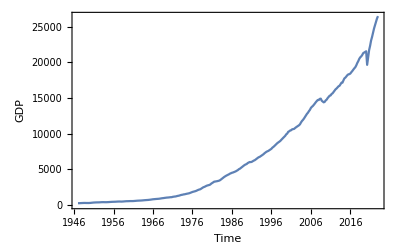

TimeSeries[…]

TimeSeriesModel[…]

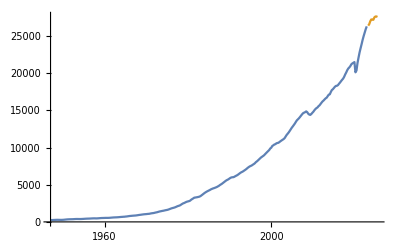

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

DateListPlot::ldata: TimeSeriesModel[Automatic,{«1»}] is not a valid dataset or list of datasets.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

DateListPlot::ldata: TimeSeriesModel[Automatic,{«1»}] is not a valid dataset or list of datasets.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Show::gcomb: Could not combine the graphics objects in Show[DateListPlot[«1»],,PlotLabel→tsm Model and Tester2 Scatterplot,PlotLegends→{tsm,Tester2}].

Show[DateListPlot[TimeSeriesModel[…],PlotStyle→RGBColor[1, 0, 0],PlotRange→All],-Graphics-,PlotLabel→tsm Model and Tester2 Scatterplot,PlotLegends→{tsm,Tester2}]

```mathematica
whole2=preprocessedData;
{trainer2,tester2}=ResourceFunction["TrainTestSplit"][(#1->#2)&@@#&/@Drop[#&@@whole2,11],Shuffle->True];
DateListPlot[TimeSeries[trainer2],FrameLabel->{"Time","GDP"}]
ts=TimeSeries[trainer2];
resampledTS=TimeSeriesResample[ts]
tsm=TimeSeriesModelFit[resampledTS]

ListLinePlot[{tsm["TemporalData"],TimeSeriesForecast[tsm,{10}]}] 


(*Step 2:DateListPlot for the model*)
plot1=DateListPlot[tsm,PlotStyle->Red,PlotRange->All];

(*Step 3:ListPlot for the scatterplot*)
plot2=ListPlot[tester2,PlotStyle->Blue];

(*Step 4:Combine plots using Show*)
Show[plot1,plot2,PlotLabel->"tsm Model and Tester2 Scatterplot",PlotLegends->{"tsm","Tester2"}]
(*the next 5 steps*)
```

## Using Neural Networks

```mathematica
whole2=preprocessedData;
{trainer2,tester2}=ResourceFunction["TrainTestSplit"][(#1->#2)&@@#&/@Drop[#&@@whole2,11],Shuffle->True];(*And the date values are stored in the first element of each example*)

(*Preprocessing to convert date objects to numerical values*)preprocessedTrain=Transpose[{DateValue[#[[1]],"UnixTimestamp"],#[[2]]}&/@trainer3];
preprocessedTest=Transpose[{DateValue[#[[1]],"UnixTimestamp"],#[[2]]}&/@tester3];

First[preprocessedTrain]

net=NetChain[{LinearLayer[15],BatchNormalizationLayer[],ElementwiseLayer[Sigmoid],LinearLayer[10],BatchNormalizationLayer[],ElementwiseLayer[Sigmoid],LinearLayer[1]},"Input"->1,"Output"->"Scalar"]

results=NetTrain[net,preprocessedTrain,All,ValidationSet->preprocessedTest,Method->"Adam"]

{trainedNet,valLosses}=results[{"TrainedNet","ValidationLossList"}]
Min[valLosses]

trainedNet[{DateValue[trainer3[[1,1]],"UnixTimestamp"]}]

p=Predict[preprocessedTrain,PerformanceGoal->"Quality"]
pm=PredictorMeasurements[p,preprocessedTest,"MeanSquare"]
```

NetTrain::invtdata: Training data should be an association of lists, or a rule from input to output examples.

$Failed

NetExtract::arg1: First argument $Failed should be a net, NetEncoder, or NetDecoder.

$Failed[ValidationLoss]

$Failed[ValidationLoss]